```mathematica
(*{epsilon0,species,int_on,OVIcov,FOGcov,LARcov,BIOcov,SREcov,IRScov,ITNcov,ECScov,ECTcov,HOUcov,OBTcov,SPRcov,PPMcov,ATSBcov,SSPcov}*)
eirValues={1,10,50,100};
species={1,2,3};
tuplesKey={houCov,ppmCov,atsbCov,irsCov,larCov,ectCov}={.4,.5,.4,.8,.8,.4};
tuples=Tuples[ConstantArray[{0,1},6]];
```

```mathematica
(*{
1.OVIcov,
2.FOGcov,
3.LARcov*,
4.BIOcov,
5.SREcov,
6.IRScov*,
7.ITNcov,
8.ECScov,
9.ECTcov*,
10.HOUcov*,
11.OBTcov,
12.SPRcov,
13.PPMcov*,
14.ATSBcov*,
15.SSPcov
}*)
codedValues=Table[i*tuplesKey,{i,tuples}];
```

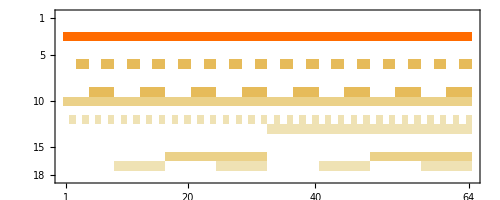

```mathematica
constants=ConstantArray[ConstantArray[0,18],Length[codedValues]];
pairs=Transpose[{constants,codedValues}];
interventionsSet=ReplacePart[#[[1]],{3->10,7+3->.5,10+3->#[[2,1]],13+3->#[[2,2]],14+3->#[[2,3]],6+3->#[[2,4]],3+3->#[[2,5]],9+3->#[[2,6]]}]&/@pairs;
MatrixPlot[interventionsSet//Transpose]
```

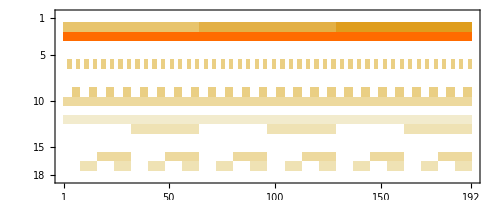

```mathematica
interventionsWithSpecies=Flatten[Table[ReplacePart[#,2->i]&/@interventionsSet,{i,1,3}],1];
MatrixPlot[interventionsWithSpecies//Transpose]
```

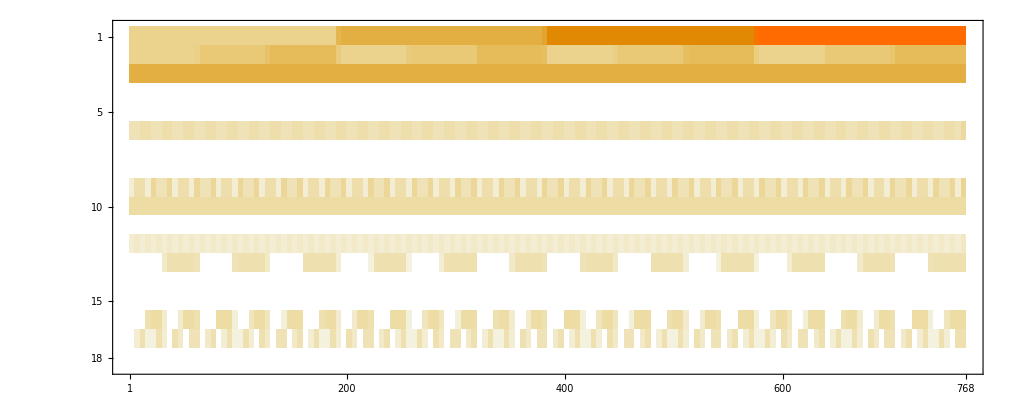

```mathematica
interventionsWithEIR=Flatten[Table[ReplacePart[#,1->i]&/@interventionsWithSpecies,{i,eirValues}],1];
MatrixPlot[interventionsWithEIR//Transpose]
```

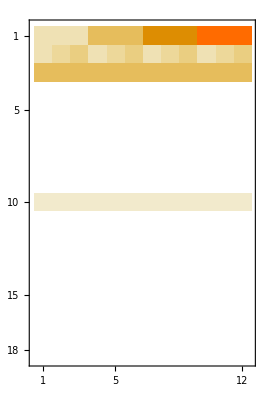

```mathematica
interventionsWithSpecies2=Flatten[Table[ReplacePart[#,2->i]&/@{{0,0,10,0,0,0,0,0,0,.8,0,0,0,0,0,0,0,0}},{i,1,3}],1];
MatrixPlot[interventionsWithSpecies2//Transpose];
interventionsWithEIR2=Flatten[Table[ReplacePart[#,1->i]&/@interventionsWithSpecies2,{i,eirValues}],1];
MatrixPlot[interventionsWithEIR2//Transpose]
```

{{1,1,10,0,0,0,0,0,0,0.8,0,0,0,0,0,0,0,0},{1,2,10,0,0,0,0,0,0,0.8,0,0,0,0,0,0,0,0},{1,3,10,0,0,0,0,0,0,0.8,0,0,0,0,0,0,0,0},{10,1,10,0,0,0,0,0,0,0.8,0,0,0,0,0,0,0,0},{10,2,10,0,0,0,0,0,0,0.8,0,0,0,0,0,0,0,0},770,{100,3,10,0,0,0.8,0,0,0.,0.5,0,0.4,0.4,0,0,0.5,0.4,0},{100,3,10,0,0,0.,0,0,0.8,0.5,0,0.,0.4,0,0,0.5,0.4,0},{100,3,10,0,0,0.,0,0,0.8,0.5,0,0.4,0.4,0,0,0.5,0.4,0},{100,3,10,0,0,0.8,0,0,0.8,0.5,0,0.,0.4,0,0,0.5,0.4,0},{100,3,10,0,0,0.8,0,0,0.8,0.5,0,0.4,0.4,0,0,0.5,0.4,0}}
 |  |  |  |

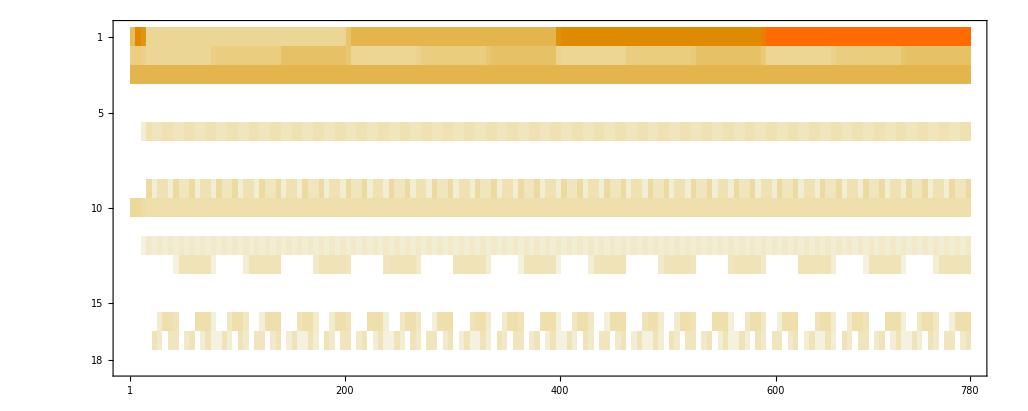

/Users/chipdelmal/Desktop

sweeeeeep.csv

```mathematica
finalTuples=Flatten[{interventionsWithEIR2,interventionsWithEIR},1]
MatrixPlot[finalTuples//Transpose]
SetDirectory[NotebookDirectory[]]
Export["sweeeeeep.csv",finalTuples]
```